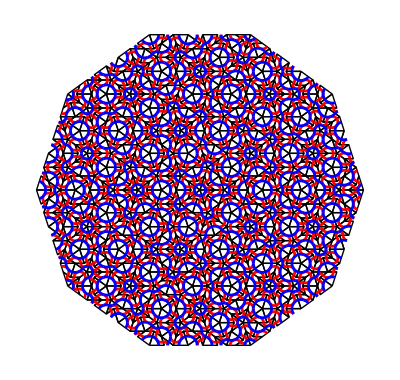

```mathematica
ResourceFunction["PenroseTile"]["Sun",5]
```

```mathematica
gm=-Graphics-;
```

```mathematica
PolyhedronData[{"Prism",10},"Faces"]
```

GraphicsComplex[{{1/2 (-1-√5),0,-1/2},{1/2 (-1-√5),0,1/2},{1/2 (1+√5),0,-1/2},{1/2 (1+√5),0,1/2},{1/8 (-1-√5) (1+√5),-1/2 √(5/8-(√5)/8) (1+√5),-1/2},{1/8 (-1-√5) (1+√5),-1/2 √(5/8-(√5)/8) (1+√5),1/2},{1/8 (-1-√5) (1+√5),1/2 √(5/8-(√5)/8) (1+√5),-1/2},{1/8 (-1-√5) (1+√5),1/2 √(5/8-(√5)/8) (1+√5),1/2},{1/8 (1-√5) (1+√5),-1/2 √(5/8+(√5)/8) (1+√5),-1/2},{1/8 (1-√5) (1+√5),-1/2 √(5/8+(√5)/8) (1+√5),1/2},{1/8 (1-√5) (1+√5),1/2 √(5/8+(√5)/8) (1+√5),-1/2},{1/8 (1-√5) (1+√5),1/2 √(5/8+(√5)/8) (1+√5),1/2},{1/8 (-1+√5) (1+√5),-1/2 √(5/8+(√5)/8) (1+√5),-1/2},{1/8 (-1+√5) (1+√5),-1/2 √(5/8+(√5)/8) (1+√5),1/2},{1/8 (-1+√5) (1+√5),1/2 √(5/8+(√5)/8) (1+√5),-1/2},{1/8 (-1+√5) (1+√5),1/2 √(5/8+(√5)/8) (1+√5),1/2},{1/8 (1+√5)^2,-1/2 √(5/8-(√5)/8) (1+√5),-1/2},{1/8 (1+√5)^2,-1/2 √(5/8-(√5)/8) (1+√5),1/2},{1/8 (1+√5)^2,1/2 √(5/8-(√5)/8) (1+√5),-1/2},{1/8 (1+√5)^2,1/2 √(5/8-(√5)/8) (1+√5),1/2}},Polygon[{{17,13,9,5,1,7,11,15,19,3},{4,20,16,12,8,2,6,10,14,18},{3,19,20,4},{19,15,16,20},{15,11,12,16},{11,7,8,12},{7,1,2,8},{1,5,6,2},{5,9,10,6},{9,13,14,10},{13,17,18,14},{17,3,4,18}}]]

```mathematica
v={{1/2 (-1-√5),0,-1/2},{1/2 (-1-√5),0,1/2},{1/2 (1+√5),0,-1/2},{1/2 (1+√5),0,1/2},{1/8 (-1-√5) (1+√5),-1/2 √(5/8-(√5)/8) (1+√5),-1/2},{1/8 (-1-√5) (1+√5),-1/2 √(5/8-(√5)/8) (1+√5),1/2},{1/8 (-1-√5) (1+√5),1/2 √(5/8-(√5)/8) (1+√5),-1/2},{1/8 (-1-√5) (1+√5),1/2 √(5/8-(√5)/8) (1+√5),1/2},{1/8 (1-√5) (1+√5),-1/2 √(5/8+(√5)/8) (1+√5),-1/2},{1/8 (1-√5) (1+√5),-1/2 √(5/8+(√5)/8) (1+√5),1/2},{1/8 (1-√5) (1+√5),1/2 √(5/8+(√5)/8) (1+√5),-1/2},{1/8 (1-√5) (1+√5),1/2 √(5/8+(√5)/8) (1+√5),1/2},{1/8 (-1+√5) (1+√5),-1/2 √(5/8+(√5)/8) (1+√5),-1/2},{1/8 (-1+√5) (1+√5),-1/2 √(5/8+(√5)/8) (1+√5),1/2},{1/8 (-1+√5) (1+√5),1/2 √(5/8+(√5)/8) (1+√5),-1/2},{1/8 (-1+√5) (1+√5),1/2 √(5/8+(√5)/8) (1+√5),1/2},{1/8 (1+√5)^2,-1/2 √(5/8-(√5)/8) (1+√5),-1/2},{1/8 (1+√5)^2,-1/2 √(5/8-(√5)/8) (1+√5),1/2},{1/8 (1+√5)^2,1/2 √(5/8-(√5)/8) (1+√5),-1/2},{1/8 (1+√5)^2,1/2 √(5/8-(√5)/8) (1+√5),1/2}};
```

```mathematica
i={{17,13,9,5,1,7,11,15,19,3},{4,20,16,12,8,2,6,10,14,18},{3,19,20,4},{19,15,16,20},{15,11,12,16},{11,7,8,12},{7,1,2,8},{1,5,6,2},{5,9,10,6},{9,13,14,10},{13,17,18,14},{17,3,4,18}};
```

```mathematica
g1=Graphics3D[{Blue,Opacity[1],Specularity[White,20],Texture[gm],GraphicsComplex[v,Polygon[i]],(Append[#1,{VertexTextureCoordinates->With[{n=Length[First[#1]]},ParallelTable[(1/2 {Cos[2 π i/n],Sin[2 π i/n]}+{1/2,1/2}),{i,0,n-1}]]}]&)/@Flatten[Normal[PolyhedronData[{"Prism",10},"Faces"]]]},Boxed->False,ViewPoint->{2,2,2},ImageSize->{2000,2000},Background->White];
```

```mathematica
g2=Show[g1,ViewPoint->Above,ImageSize->{2000,2000}];
```

```mathematica
g3=Show[g1,ViewPoint->{1.3, -2.4, 2.},ImageSize->{2000,2000}];
```

```mathematica
g4=Show[g1,ViewPoint->{1.,-2,-2},ImageSize->{2000,2000}];
```

```mathematica
Export["Prism10_PenroseTile_Sun_BackgroundWhite_Grid.jpg",Rasterize[GraphicsGrid[{{g1,g2},{g3,g4}}],"Image",ImageSize->4000]];
```

```mathematica
(*end*)
```